```mathematica
{{2+3}, {□}}
```

{{5},{□}}

```mathematica
5+6
```

11

```mathematica
2^3
```

8

```mathematica
Limit[1/x,x->Infinity]
```

0

```mathematica
DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

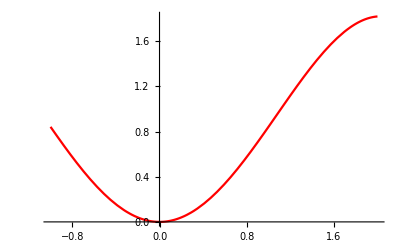

```mathematica
Plot[x*Sin[x],{x,-1,2},PlotStyle->Red]
```

```mathematica
-(2-1^(1/12)((-1)^(5/6)tan^-1(((-1)^(5/12)(2+(1-i √3)tan(x/2)))/(2 3^(1/4)))+tan^-1(((-1)^(7/12)(2+(1+i √3)tan(x/2)))/(2 3^(1/4)))))/3^(3/4)+C
```

```mathematica
Integrate[(1-Sin[x])/(1-Sin[x]^3),x]
```

-1/3 ⅈ (√(-6+2 ⅈ √3) ArcTan[(2+(1-ⅈ √3) Tan[x/2])/(√(-6-2 ⅈ √3))]-√(-6-2 ⅈ √3) ArcTan[(2+(1+ⅈ √3) Tan[x/2])/(√(-6+2 ⅈ √3))])

```mathematica
∫(1-sin(x))/(1-sin^3(x))ⅆx
```

-1/3 ⅈ (√(-6+2 ⅈ √3) ArcTan[(2+(1-ⅈ √3) Tan[x/2])/(√(-6-2 ⅈ √3))]-√(-6-2 ⅈ √3) ArcTan[(2+(1+ⅈ √3) Tan[x/2])/(√(-6+2 ⅈ √3))])

```mathematica
Style[" 你好\nLaTeX"]//TeXForm
```

\text{ $\unicode{4f60}\unicode{597d}\backslash $nLaTeX}

```mathematica
pts={{1,1},{2,3},{3,-1},{4,1},{5,0}};
```

```mathematica
f=BSplineFunction[pts]
```

BSplineFunction[…]

```mathematica
f[.5]
```

{3.,0.5}

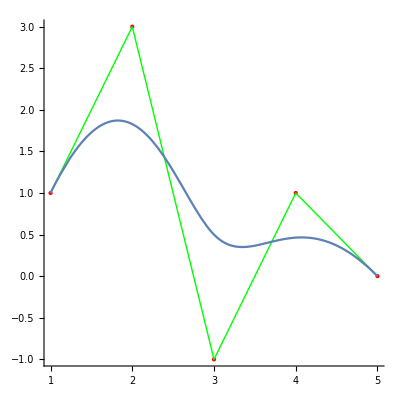

```mathematica
Show[Graphics[{Red,Point[pts],Green,Line[pts]},Axes->True],ParametricPlot[f[t],{t,0,1}]]
```

```mathematica
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts]}],Graphics3D[{Gray,Line[pts],Gray,Line[Transpose[pts]]}],ParametricPlot3D[f[u,v],{u,0,1},{v,0,1}]]
```

-Graphics3D-

```mathematica
Graphics3D[{Gray,Line[pts],Gray,Line[Transpose[pts]]}]
```

```mathematica
Table[Graphics3D[{Yellow,Opacity[.8],PolyhedronData[p,"GraphicsComplex"]}],{p,{"Dodecahedron","Icosahedron","TruncatedIcosahedron"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

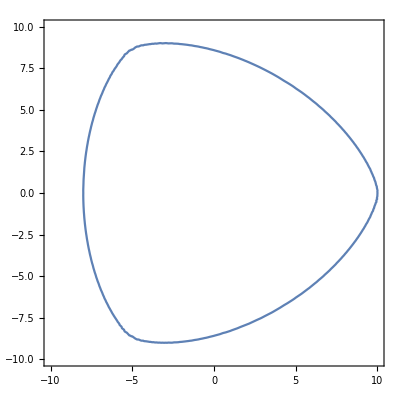

```mathematica
ContourPlot[(x^2+y^2)^4-45 (x^2+y^2)^3-41283 (x^2+y^2)^2+7950960 (x^2+y^2)+16 (x^2-3 y^2)^3+48 (x^2+y^2) (x^2-3 y^2)^2-720^3+(x^2-3 y^2) x (16 (x^2+y^2)^2-5544 (x^2+y^2)+266382)==0,{x,-10,10},{y,-10,10}]
```

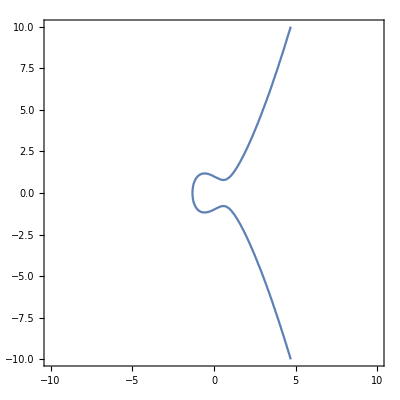

```mathematica
ContourPlot[y^2==x^3-x+1, {x,-10,10},{y,-10,10}]
```

```mathematica
HarmonicMean[{a,b,c,d}]
```

4/(1/a+1/b+1/c+1/d)

```mathematica
RootMeanSquare[ {a,b,c,d}]
```

1/2 √(a^2+b^2+c^2+d^2)